```mathematica
D[√(x/4)*0.2+0.8,x]/0.2
```

0.25/(√x)

```mathematica
Integrate[x*D[√(x/4)*0.2+0.8,x],{x,0,4}]//N
```

0.266667

```mathematica
Integrate[(x-0.26666666666666666)^2*D[√(x/4)*0.2+0.8,x],{x,0,4}]
```

0.512

```mathematica
0.26666666666666666/0.2
```

1.33333

```mathematica
Integrate[x*D[√(x/4)*0.2+0.8,x]/0.2,{x,0,4}]
```

1.33333

```mathematica
Solve[√(x/4)*0.2+0.8==0.95,x]
```

{{x→2.25}}

```mathematica
f[x_]:=D[√(x/4)*0.2+0.8,x]
```

```mathematica
1/Integrate[f[x],{x,2,4}]*Integrate[x*f[x],{x,2,4}]
```

2.94281

```mathematica
1 - (10*(0+1)^4)^-1//N
```

0.9

```mathematica
(1 - (10*(x+1)^4)^-1-1 - 0.9)/(1-0.9)
```

10. (-0.9-1/(10 (1+x)^4))

```mathematica
F[x_]:=(10*(x+1)^4)^-1
```

```mathematica
Integrate[x*D[F[x],x],{x,0,Infinity}]
```

-1/30

```mathematica
(-1/30)/(1-0.9)
```

-0.333333

```mathematica
Integrate[(x+1/30)^2*D[F[x],x],{x,0,Infinity}]//N
```

-0.0356667

```mathematica
p1 = 0.2
p2=0.1
```

0.2

0.1

```mathematica
F[x_]:=p1/(p1+p2)*(1-ⅇ^-x)+p2/(p1+p2)*(1-ⅇ^(-2x))
```

```mathematica
Integrate[x*D[F[x],x],{x,0,Infinity}]
```

0.833333

```mathematica
Integrate[(x-0.8333333333333333)^2*D[F[x],x],{x,0,Infinity}]
```

0.805556

```mathematica
F[x_]:=PDF[NormalDistribution[10,1],x]
```

```mathematica
Clear[Fs]
Fs[x_]:=0.7+0.2*CDF[NormalDistribution[10,1],x] +0.1*CDF[NormalDistribution[20,2],x]
```

```mathematica
D[Fs[x],x]
```

0.0797885 ⅇ^(-1/2 (10-x)^2)+0.0199471 ⅇ^(-1/8 (20-x)^2)

```mathematica
u[x_]:=0.7+0.07978845608028655 ⅇ^(-1/2 (10-x)^2)+0.019947114020071637 ⅇ^(-1/8 (20-x)^2)
```

```mathematica
Table[u[r],{r,-2,2}]
```

{1.05945×10^-28,2.33006×10^-26,1.92365×10^-23,2.06099×10^-19,1.01051×10^-15}

```mathematica
o[x_]:=Boole[x≥0]
```

```mathematica
Clear[]
jk[x_]:=D[Fs[x],x]
```

```mathematica
jk[x]
```

0.0797885 ⅇ^(-1/2 (10-x)^2)+0.0199471 ⅇ^(-1/8 (20-x)^2)

```mathematica
Table[u[r],{x,-1,1}]
```

{0.0797885 ⅇ^(-1/2 (10-r)^2)+0.0199471 ⅇ^(-1/8 (20-r)^2),0.0797885 ⅇ^(-1/2 (10-r)^2)+0.0199471 ⅇ^(-1/8 (20-r)^2),0.0797885 ⅇ^(-1/2 (10-r)^2)+0.0199471 ⅇ^(-1/8 (20-r)^2)}

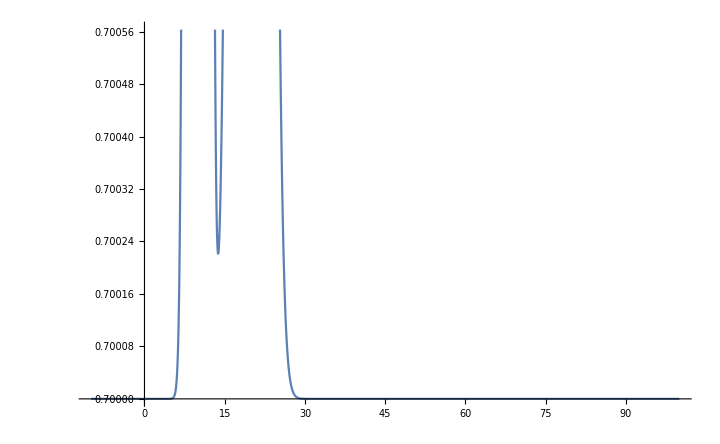

```mathematica
Plot[u[x],{x,-10,100}]
```

```mathematica
Integrate[D[Fs[x],x],{x,-Infinity,Infinity}]
```

0.3

```mathematica
Total[{0.7,0.2,0.1}*{0,1,2}]
```

0.4

```mathematica
Total[({0,1,2}-0.4)^2*{0.7,0.2,0.1}]
```

0.44

```mathematica
100*0.44+1.04
```

45.04